## g

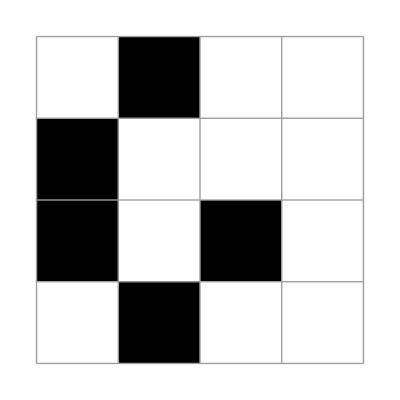
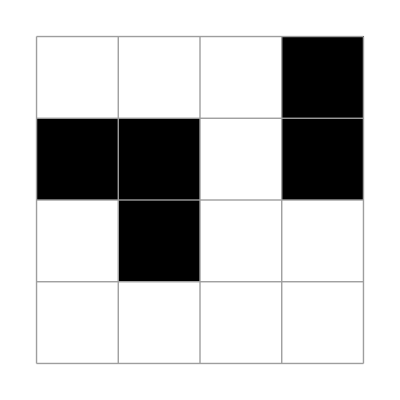
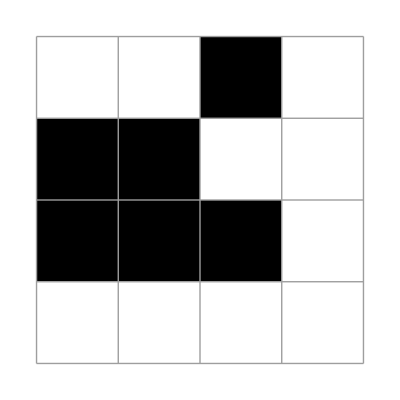
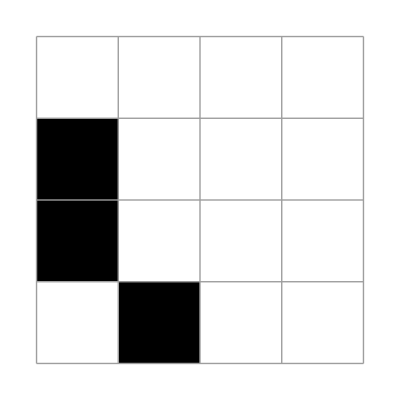
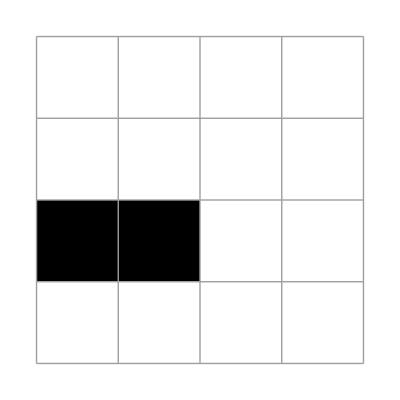
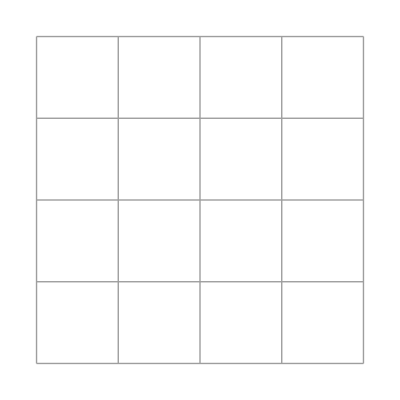
{0.815344,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

## o

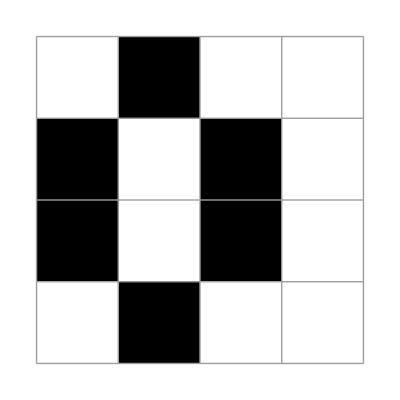
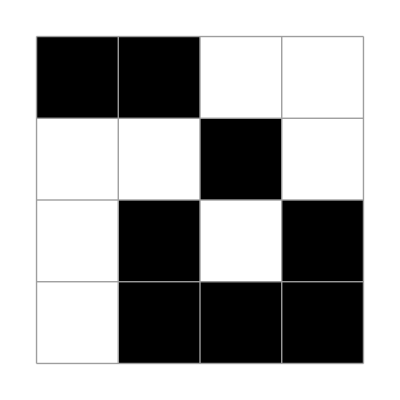
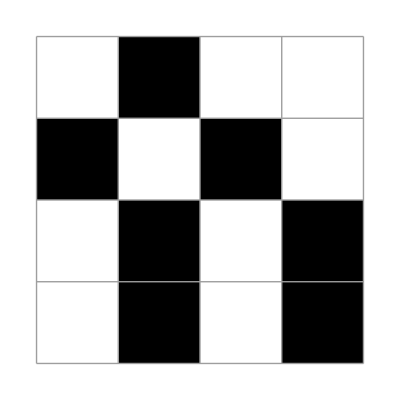
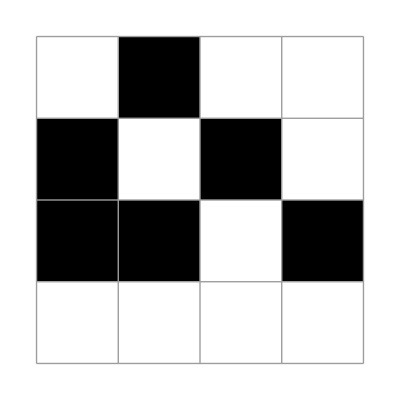
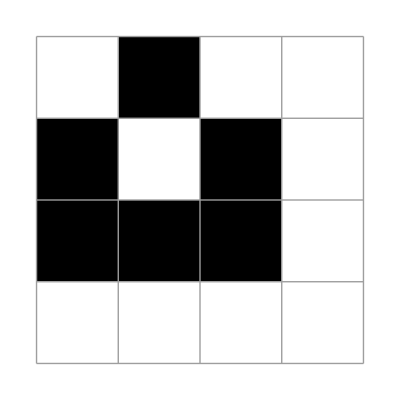
{0.944615,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

## t

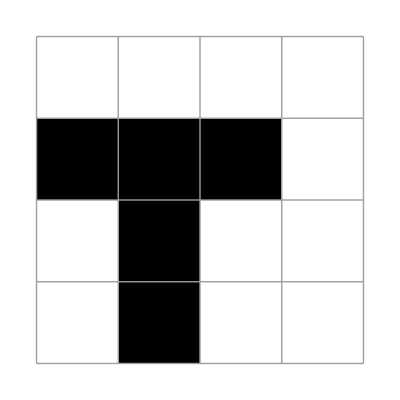
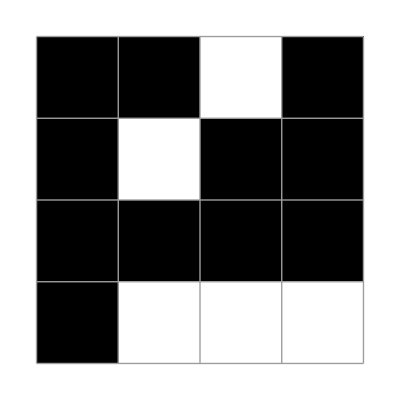
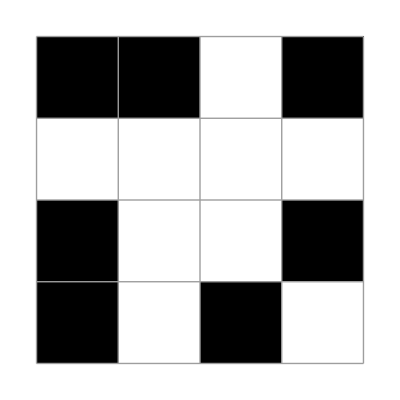
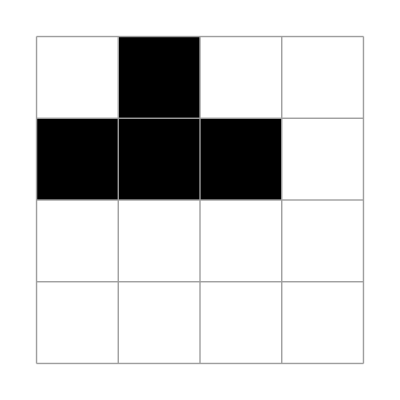
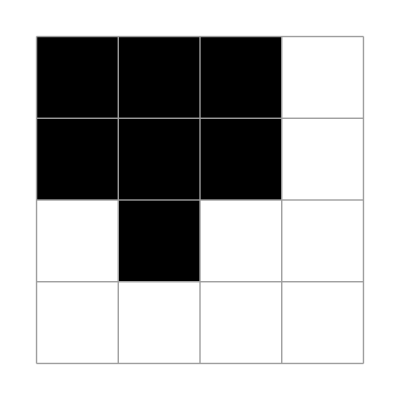
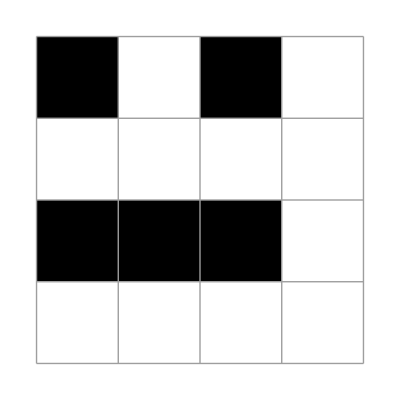
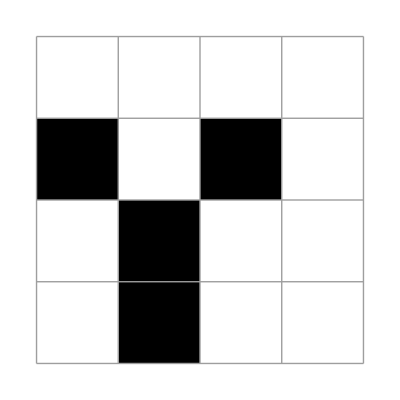
{0.821533,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

## z

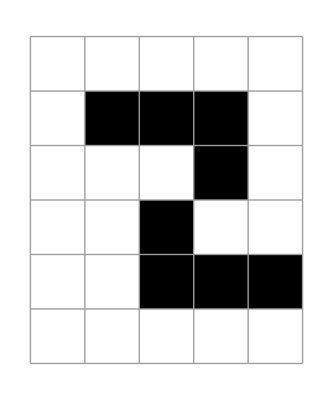
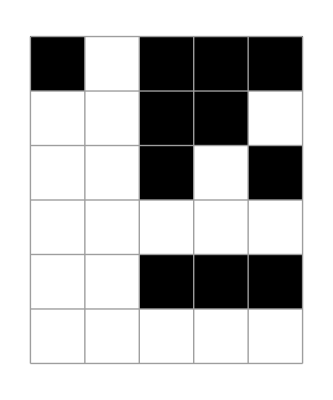
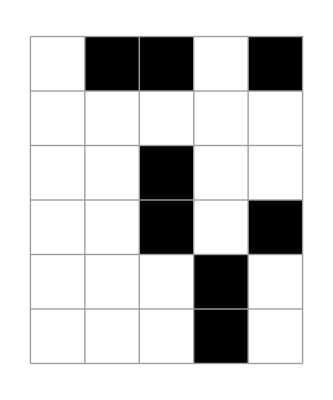
{2.99399,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
({{0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 1, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 1, 1}, {0, 0, 0, 0, 0}})//plt
```

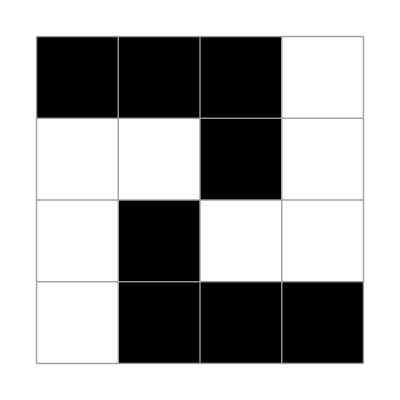

```mathematica
({{1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 1, 1, 1}})//plt
```

```mathematica
NestWhileList
```

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/00_still_life_stack_question/001_counting_function/countModule3.m"];
LIFE=({{0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 1, 0}, {0, 0, 1, 0, 0}, {0, 0, 1, 1, 1}, {0, 0, 0, 0, 0}});
(*xPArray=RandomInteger[{0,1},{6,6}];
*)(*updateIJ[xPArray]*)
AbsoluteTiming[{LIFE//plt,rollBackPlot[LIFE,2]}]
```

{2.99399,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Clear[x,i,j];Evaluate[BooleanCountingFunction[{0,5},Array[x,{3,3}]]]
```

True

```mathematica
form[xpArray_]:=Module[{formulaIJ,formula,varlist,out1,asdf,xp,i,j},{i,j}=Dimensions[xpArray];
x[_,0]=False;
x[0,_]=False;
x[_,j+1]=False;
x[i+1,_]=False;
Evaluate[Array[xp,{i,j}]]=loob[xpArray];
(**)(*({*)(*{xp[1,1],xp[1,2],xp[1,3],xp[1,4],xp[1,5]},*)(*{xp[2,1],xp[2,2],xp[2,3],xp[2,4],xp[2,5]},*)(*{xp[3,1],xp[3,2],xp[3,3],xp[3,4],xp[3,5]},*)(*{xp[4,1],xp[4,2],xp[4,3],xp[4,4],xp[4,5]},*)(*{xp[5,1],xp[5,2],xp[5,3],xp[5,4],xp[5,5]}*)(*})=loob[xpArray];*)formulaIJ=(and@{Nothing,(x[##]&&count[{0},{##}])~Implies~!xp[##],(x[##]&&count[{1},{##}])~Implies~!xp[##],(x[##]&&count[{2},{##}])~Implies~xp[##],(x[##]&&count[{3},{##}])~Implies~xp[##],(x[##]&&count[{4},{##}])~Implies~!xp[##],(x[##]&&count[{5},{##}])~Implies~!xp[##],(x[##]&&count[{6},{##}])~Implies~!xp[##],(x[##]&&count[{7},{##}])~Implies~!xp[##],(x[##]&&count[{8},{##}])~Implies~!xp[##]
(*not*),(!x[##]&&count[{0},{##}])~Implies~!xp[##],(!x[##]&&count[{1},{##}])~Implies~!xp[##],(!x[##]&&count[{2},{##}])~Implies~!xp[##],(!x[##]&&count[{3},{##}])~Implies~xp[##],(!x[##]&&count[{4},{##}])~Implies~!xp[##],(!x[##]&&count[{5},{##}])~Implies~!xp[##],(!x[##]&&count[{6},{##}])~Implies~!xp[##],(!x[##]&&count[{7},{##}])~Implies~!xp[##],(!x[##]&&count[{8},{##}])~Implies~!xp[##]})&;
formula=BooleanConvert[and@Flatten@Array[formulaIJ,{i,j}],"CNF"]];
f=form[({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}})];
f
```

(!x[1,1]||!x[1,2])&&(x[1,1]||x[1,2])&&(!x[1,2]||x[3,1])&&(x[1,2]||!x[3,1])&&x[1,3]&&!x[2,1]&&!x[2,2]&&!x[2,3]&&(!x[3,1]||!x[3,2])&&(x[3,1]||x[3,2])&&x[3,3]

```mathematica
Expectation[x,x\[Distributed]ProbabilityDistribution[n x^(n-1)/θ^n,{x,0,θ}]]
```

(n θ)/(1+n)